# Global Optimization

## Illustrative Cases I-IV

This notebook checks whether the RE processes simulated in the four illustrative cases lead to global optima and full RE states. Moreover, it visualizes various properties of the set of global optima in function of the weights of the achievement function.

## Load packages

```mathematica
SetDirectory[$HomeDirectory];
If[!MemberQ[$Path,#],AppendTo[$Path, #]]&[FileNameJoin[{"git","remoma","packages","DialecticalStructures"}]];
If[!MemberQ[$Path,#],AppendTo[$Path, #]]&[FileNameJoin[{"git","remoma","packages","ReflectiveEquilibrium"}]];
<<DialecticalStructures`BasicTDS`;
<<DialecticalStructures`InductiveReasoning`;
<<DialecticalStructures`PositionsAnalytics`;
<<ReflectiveEquilibrium`ReflectiveEquilibrium`;
```

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory[".."];
If[!DirectoryQ["results"], CreateDirectory["results"]];
SetDirectory["results"];
```

## Setting up the scene

These are the parameters we use:

```mathematica
parameters=<|
		"numSen"->7,
		"accountFunction"->"NormalizedCloseness",
		"alpha"->0.4,
		"beta"->0.8,
		"ConflictPenalty"->1,"ContractionPenalty"->1,"ExpansionPenalty"->0,
		"ExpansionPenaltyAccount"->0.3,
		"nMax"->10
	|>;
```

Let tau and C_0 be given. These are our four standard illustrative cases:

```mathematica
RandomTau[5,1,Range[7]]
```

(6⇒2)&&(3⇒!7)&&(!7⇒4)&&(!5⇒!6)&&(5⇒6)

```mathematica
tau=(1⇒3)&&(1⇒4)&&(1⇒5)&&(1⇒!6)&&(2⇒5)&&(2⇒6)&&(2⇒7)&&(2⇒!4);
senIDs=Range[Lookup[parameters,"numSen",8]];
initialComs={118,121,1090,1333};
IntegerToList[#,senIDs]&/@initialComs
```

{{3,4,5},{2,3,4,5},{3,4,5,6,7},{3,4,5,7,!6}}

We say that P is the set of all permissible theory-commitment pairs <T,C>, where such a pair is permissible iff C is minimally consistent and T is consistent and closed. (Claus is right in saying that we’ve defined the notions of theory and commitments such that <T,C>-pairs are permissible.) Furthermore, let T be the set of all consistent and closed theories, and C be the set of all minimally consistent commitments. C is the list Range[3^7] (integer-representation of partial positions). T is a subset of C. P is hence a list of integer-pairs.

We calculate sigma, nPrinciples and closedPositions. (These objects are defined in the packages and will be used to speed up calculations.)

```mathematica
PrintTemporary["Creating sigma..."];
sigma = Sigma[tau, True, senIDs];
PrintTemporary["...done."];
 
PrintTemporary["Creating nPrinciples..."];
nPrinciples = NPrinciples[sigma, senIDs];
PrintTemporary["...done."];

PrintTemporary["Creating closedPositions..."];
closedPositions = DeleteCases[DialecticallyClosedPositions[tau, True, senIDs],1];
PrintTemporary["...done."];
```

We further calculate

for every T in T: Simplicity[T] and store the results in SparseArray Simp. (Simplicity[T] is stored in Simp at position T.)

```mathematica
Simp=SparseArray[#->Simplicity[#,nPrinciples[[ # ]],senIDs]&/@closedPositions];
```

for every C in C and for every C_0^i in initialComs: Closeness[C,C_0] and store the results in SparseArray Clos[[i]]. (Closeness[C,C_0^i] is stored in Clos[[i]] at position C.)

```mathematica
Clos=Map[
Function[
initialCom,
SparseArray[#->Closeness[#,initialCom,senIDs,KeyTake[parameters,{"ConflictPenalty","ContractionPenalty","ExpansionPenalty"}]]&
/@Range[3^Length[senIDs]]
]
],
initialComs
];
```

for every <T,C> in P: Account[T,C] and store the results in SparseArray Acco. (Account[T,C] is stored in Acco at position {T,C}.)

```mathematica
Account=AccountFunction[parameters];
```

```mathematica
Acco=Monitor[
SparseArray[
Flatten[Table[
{closedPositions[[i]],c}->Account[c,closedPositions[[i]],sigma,senIDs],
{i,Length[closedPositions]},{c,3^Length[senIDs]}
],
1
]
],
ProgressIndicator[i,{1,Length[closedPositions]}]
];
```

Every <T,C> pair is mapped to a triple <Simplicity[T], Closeness[C,C_0], Account[T,C]>. We call such a triple a SCA-triple.

```mathematica
TCPtoSCAT[tcp_,caseindex_]:={
Simp[[First[tcp]]],
Clos[[caseindex,Last[tcp]]],
Acco[[First[tcp],Last[tcp]]]
};
```

## Pareto Frontiers

The array paretosets stores for each illustrative case the set of all pareto optimal SCA-triples. It is updated whenever the function PlotParetoFrontier[i] is called.

```mathematica
paretosets={{},{},{},{}};
```

In addition, the array paretoTCPairs stores for each illustrative case the set of all pareto optimal <T,C>-pairs. These are the TC-apirs that are mapped to pareto-optimal SCA-tuples.

```mathematica
paretoTCPairs={{},{},{},{}};
```

We plot all <T,C>-pairs in P in

an Agreement-Simplicity-Closeness Space

```mathematica
DominatesQ[p1_,p2_]:=(And@@((First[#]≥Last[#])&/@Transpose[{p1,p2}]))&&p1≠p2;(*this function is not needed anymore*)
```

Attention: Pareto optimal TC-pairs do not belong necessarily to the convex hull of the point-set!! This was a mistake in an earlier version.

```mathematica
PlotParetoFrontier[caseindex_]:=Module[{pts,px,py,pz,convexhull,convexhullmesh,paretoindices,highlightcellindices,paretoset},
PrintTemporary["Set up list of SCA-tuples..."];
pts=TCPtoSCAT[#,caseindex]&
/@Tuples[{closedPositions,Range[3^Length[senIDs]]}];(*all TC-pairs*)

PrintTemporary["Calculating Convex Hull..."];
convexhullmesh=ConvexHullMesh[pts];
convexhull=MeshCoordinates[convexhullmesh];

PrintTemporary["Calculating Pareto Optimal Points..."];
(*Old, problematic implmentation, because only convex hull considered!*)
(*
paretoset=Complement[
convexhull,
Select[Tuples[convexhull,2],DominatesQ[First[#],Last[#]]&][[All,2]]
];
*)
paretoset=-Internal`ListMin[-pts];
paretosets[[caseindex]]=paretoset;(*Store the calcualted pareto set in the global variable*)

paretoindices=Flatten[Intersection[paretoset,convexhull]/.PositionIndex[convexhull]];

PrintTemporary["Calculating MeshCells to be highlighted..."];
highlightcellindices=
MeshCellIndex[
convexhullmesh,
Select[
Union[
MeshCells[convexhullmesh,1],
MeshCells[convexhullmesh,2]
],
SubsetQ[paretoindices,First[Level[#,1]]]&
]
];

PrintTemporary["Plotting..."];
GraphicsColumn[{
Show[
ListPointPlot3D[paretoset,PlotRange->{{0.3,1.01},{0.7,1.01},{0,1.01}},AspectRatio->1,AxesLabel->{"Simp","Clos","Acco"}],
HighlightMesh[ConvexHullMesh[pts,MeshCellStyle->Opacity[0.05]],Style[#,Opacity[0.7]]&/@highlightcellindices,PlotTheme->"Detailed"],
Graphics3D[{Red,PointSize[Large],Point[paretoset]}]
]
}]
];
```

The above function generates a plot which visualizes the Pareto Frontiers, and hence the trade-offs involved.

The following functions calculate the pareto efficient TC-pairs.

```mathematica
ParetoTCPairs[i_]:=ParetoTCPairs[i,{1,1,1}];
ParetoTCPairs[i_,v_]:=ParetoTCPairs[i,v,paretosets[[i]]];
ParetoTCPairs[i_,v_,pset_]:=Select[
Tuples[{closedPositions,Range[3^Length[senIDs]]}],
Or@@Map[
Function[
scat,
scat==v*{
Simp[[First[#]]],
Clos[[i,Last[#]]],
Acco[[First[#],Last[#]]]
}
],
pset
]&
];
```

### Illustrative Case a

```mathematica
PlotParetoFrontier[1]
```

-Graphics-

As the plot shows, there is a single pareto-optimal <T,C>-pair. This pair is the global optimum whatever the parameters alpha and beta!

```mathematica
With[{i=1},
paretoTCPairs[[i]]=ParetoTCPairs[i]
]
```

{{611,611}}

```mathematica
IntegerToList[611,senIDs]
```

{1,3,4,5,!2,!6}

### Illustrative Case b

```mathematica
PlotParetoFrontier[2]
```

-Graphics-

Here, we have two pareto-optimal SCA-triple, generated by two <T,C>-pairs:

```mathematica
paretosets[[2]]
```

{{1,1,0.979592},{1,48/49,1.}}

```mathematica
With[{i=2},
paretoTCPairs[[i]]=ParetoTCPairs[i]
]
```

{{611,608},{611,611}}

Both pareto-optimal <T,C>-pairs in list-representation:

```mathematica
Map[IntegerToList[#,senIDs]&,{{611,608},{611,611}},{2}]
```

{{{1,3,4,5,!2,!6},{1,2,3,4,5,!6}},{{1,3,4,5,!2,!6},{1,3,4,5,!2,!6}}}

Note that, in the first of these pareto optimal <T,C> pairs, the commitments do not only diverge from the theory, even worse, they are inconsistent. We learn from this example: the weight of Account should be higher than the weight of Closeness in the objective function, otherwise we risk to end up with inconsistent commitments.

### Illustrative Case c

```mathematica
PlotParetoFrontier[3]
```

-Graphics-

Here, we have 6 pareto-optimal SCA-triple:

```mathematica
Length[paretosets[[3]]]
```

6

These are generated by 13 pareto-optimal <T,C>-pairs:

```mathematica
With[{i=3},
paretoTCPairs[[i]]=ParetoTCPairs[i]
]
```

{{611,368},{611,611},{611,1097},{611,1340},{1098,1098},{1113,1086},{1113,1095},{1113,1113},{1113,1122},{1122,1095},{1122,1122},{1340,1097},{1340,1340}}

All pareto-optimal <T,C>-pairs in list-representation:

```mathematica
Map[IntegerToList[#,senIDs]&,%,{2}]
```

{{{1,3,4,5,!2,!6},{1,3,4,5,6,!2}},{{1,3,4,5,!2,!6},{1,3,4,5,!2,!6}},{{1,3,4,5,!2,!6},{1,3,4,5,6,7,!2}},{{1,3,4,5,!2,!6},{1,3,4,5,7,!2,!6}},{{3,4,5,6,7,!1,!2},{3,4,5,6,7,!1,!2}},{{2,5,6,7,!1,!4},{2,4,5,6,7,!1}},{{2,5,6,7,!1,!4},{2,3,4,5,6,7,!1}},{{2,5,6,7,!1,!4},{2,5,6,7,!1,!4}},{{2,5,6,7,!1,!4},{2,3,5,6,7,!1,!4}},{{2,3,5,6,7,!1,!4},{2,3,4,5,6,7,!1}},{{2,3,5,6,7,!1,!4},{2,3,5,6,7,!1,!4}},{{1,3,4,5,7,!2,!6},{1,3,4,5,6,7,!2}},{{1,3,4,5,7,!2,!6},{1,3,4,5,7,!2,!6}}}

```mathematica
Length[%]
```

13

### Illustrative Case d

```mathematica
PlotParetoFrontier[4]
```

-Graphics-

Here, we have 3 pareto-optimal SCA-triple:

```mathematica
Length[paretosets[[4]]]
```

3

These are generated by 3 pareto-optimal <T,C>-pairs:

```mathematica
With[{i=4},
paretoTCPairs[[i]]=ParetoTCPairs[i]
]
```

{{611,611},{611,1340},{1340,1340}}

All pareto-optimal <T,C>-pairs in list-representation:

```mathematica
Map[IntegerToList[#,senIDs]&,%,{2}]
```

{{{1,3,4,5,!2,!6},{1,3,4,5,!2,!6}},{{1,3,4,5,!2,!6},{1,3,4,5,7,!2,!6}},{{1,3,4,5,7,!2,!6},{1,3,4,5,7,!2,!6}}}

## Lower Dimensional Pareto Optima

If all parameters in our objective function (see below) are strictly greater than 0, then the global optimum is necessary a pareto efficient <T,C>-pair. However, if some parameters equal zero (non-regular parameter combinations), non-pareto-optimal <T,C>-pairs may yield global optima, too. In that case, every global optimum is necessarily pareto-optimal in a lower-dimensional projection of the simplicity-closeness-account space. The following identifies all TC-pairs that are pareto-optimal in some lower-dimensional projection of the simplicity-closeness-account space. Global optimization with non-regular parameter combinations has to consider all these TC-pairs as candidates.

```mathematica
ldParetoTCPairs={{},{},{},{}};
```

```mathematica
ldParetoTCPairs=Module[
{pts,pset},
Table[
PrintTemporary["Caseindex "<>ToString[caseindex]];
PrintTemporary["Calculating set of SCA-tuples."];
pts=TCPtoSCAT[#,caseindex]&
/@Tuples[{closedPositions,Range[3^Length[senIDs]]}];
PrintTemporary["Calculating pareto set..."];
DeleteDuplicates[
Flatten[
Map[
Function[v,
PrintTemporary["  ... for "<>ToString[v]];
pset=-Internal`ListMin[-v#&/@pts];
ParetoTCPairs[caseindex,v,pset]
],
DeleteCases[Tuples[{1,0},3],{0,0,0}](*{{1,1,1},{1,1,0},{1,0,1},...}*)
],
1
]
],
{caseindex,4}
]
];
```

```mathematica
Length/@ldParetoTCPairs
```

{58317,40082,33997,33995}

## Global Optima

We find the set of global optima for a given parameter combination of the objective function Z. In doing so, we only consider pareto optimal TC-pairs paretoTCPairs if all parameters w_xxx have non-zero value; and we consider all lower dimensional pareto optimal TC-pairs ldParetoTCPairs otherwise.

```mathematica
ObjectiveFunction[tcp_,caseindex_,wa_,ws_]:=Module[{wc},
wc=1-(wa+ws);
ws*Simp[[First[tcp]]]+wc*Clos[[caseindex,Last[tcp]]]+wa*Acco[[First[tcp],Last[tcp]]]
];
```

Calculate weights of objective function given parameters alpha and beta of our process simulations.

Note that the simulation runs we use is 2016_09_08-0001.

```mathematica
With[
{
alpha=Lookup[parameters,"alpha"],
beta=Lookup[parameters,"beta"]
},
{
(*wa*)(alpha*beta)/(alpha+beta-alpha*beta),
(*ws*)(beta-alpha*beta)/(alpha+beta-alpha*beta)
}
]
```

{0.363636,0.545455}

The following function tests whether some TC-pair is a global optimum for the given parameters.

```mathematica
GlobalOptimumQ[tcp_,caseindex_]:=With[
{wa=0.36363636363636365,ws=0.5454545454545454},
Module[{tcpairs},
If[
wa>0&&ws>0&&(wa+ws)<1, (*If all parameters > 0*)
tcpairs=paretoTCPairs[[caseindex]], (*use pareto-optimal tcpairs,*)
tcpairs=ldParetoTCPairs[[caseindex]](*otherwise, use all low-dimensional pareto-optimal tcpairs*)
];
MemberQ[
MaximalBy[tcpairs,ObjectiveFunction[#,caseindex,wa,ws]&],
tcp
]
]
];
```

The following calculations (cases a-d below) show that our simulations of ER-processes have always delivered a global optimum given the corresponding parameters!!

#### Illustrative Case a

```mathematica
With[{ fixpoint={611,611} },
GlobalOptimumQ[fixpoint,1]
]
```

True

#### Illustrative Case b

```mathematica
With[{ fixpoint={611,611} },
GlobalOptimumQ[fixpoint,2]
]
```

True

#### Illustrative Case c

```mathematica
With[{ fixpoint={1113,1113} },
GlobalOptimumQ[fixpoint,3]
]
```

True

#### Illustrative Case d

```mathematica
With[{ fixpoint={611,611} },
GlobalOptimumQ[fixpoint,4]
]
```

True

## Parameter-Sensitivity-Studies (Ternary Plots)

!! Importantly, we only sample regular (i.e., non-zero) parameter combinations in this section !!

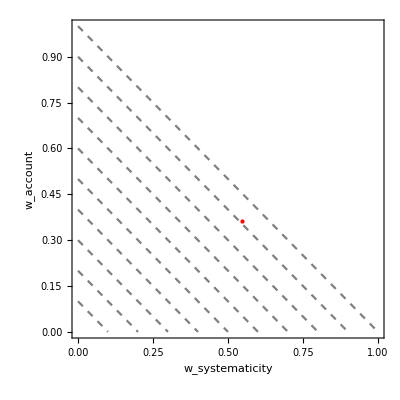

```mathematica
With[{wa=0.36363636363636365,ws=0.5454545454545454},
Show[
Table[
Plot[-x+c,{x,0,1},
PlotStyle->{Dashed,Gray},
Frame->True,
AspectRatio->1,
PlotRange->{{0,1},{0,1}},
FrameLabel->{"w_systematicity","w_account"}
],
{c,0,1,0.1}
],
Graphics[{Red,PointSize[Large],Point[{ws,wa}]}]
]
]
```

For every parameter combination of the objective function Z, we calculate the set of global optima < T, C > for each of our four cases and visualize different features of these optima (e.g., the ratio of optima such that T = C).

```mathematica
TrianglePlot[data_,label_,colorFunction_]:=
With[{wa=0.36363636363636365,ws=0.5454545454545454},
Show[
ListContourPlot[data,
PlotRange->All,
ColorFunction->colorFunction,
ColorFunctionScaling->True,
ContourStyle->None,
(*Contours->If[Length[DeleteDuplicates[  data[[All,3]]  ]]==1,{First[DeleteDuplicates[  data[[All,3]]  ]]},Automatic],*)
PlotLegends->Automatic,
FrameLabel->{"w_simplicity","w_account"},
PlotLabel->label,
ImageSize->250
],
Graphics[{White,Triangle[{{-0.01,1.01},{1.01,1.01},{1.01,-0.01}}]}],
Graphics[{Gray,Point[{ws,wa}]}],
If[Length[DeleteDuplicates[  data[[All,3]]  ]]==1,
Graphics[{Gray,Text[N[First[DeleteDuplicates[  data[[All,3]]  ]]],{0.2,0.6}]}],
Graphics[]
]
]
];
```

```mathematica
PlotData[func_]:=Module[{tcpairs},
Table[
Monitor[
Flatten[Table[
tcpairs=If[
wa>0&&ws>0&&(wa+ws)<1, (*If all parameters > 0*)
paretoTCPairs[[i]], (*use pareto-optimal tcpairs,*)
ldParetoTCPairs[[i]](*otherwise, use all low-dimensional pareto-optimal tcpairs*)
];
If[ws+wa≥1,
Nothing,
{
ws,wa,
func[MaximalBy[tcpairs,ObjectiveFunction[#,i,wa,ws]&],i]
}
],
{wa,.005,.995,.005},{ws,.005,.995,.005}
],1],
{wa,ws}
],
{i,4}
]
];
```

```mathematica
Plot4Cases[func_,param_]:=Module[{plotData,colorFunction},
colorFunction=Lookup[param,"colorFunction","Warm"];
plotData=PlotData[func];
GraphicsGrid[{
{
TrianglePlot[plotData[[1]],"Case a",colorFunction],
TrianglePlot[plotData[[2]],"Case b",colorFunction]
},
{
TrianglePlot[plotData[[3]],"Case c",colorFunction],
TrianglePlot[plotData[[4]],"Case d",colorFunction]
}
}]
];
```

NB: In the following, automatic legends for case a are flawed. (TODO: fix it manually)

### Mean Account-Value of Global Optima

```mathematica
Plot4Cases[Function[{l,i},Mean[Acco[[ First[#],Last[#] ]]&/@l]],<|"colorFunction"->"LakeColors"|>]
```

-Graphics-

### Mean Simplicity-Value of Global Optima

```mathematica
Plot4Cases[Function[{l,i},Mean[Simp[[ First[#] ]]&/@l]],<|"colorFunction"->"LakeColors"|>]
```

-Graphics-

### Mean Closeness-Value of Global Optima

```mathematica
Plot4Cases[Function[{l,i},Mean[Clos[[ i,First[#] ]]&/@l]],<|"colorFunction"->"LakeColors"|>]
```

-Graphics-

### Number of global optima

(Total number of pareto-optimal TC-pairs for c
ases a-d is, as calculated above: 1, 2, 13, 3.)

```mathematica
Plot4Cases[Function[{l,i},Length[l]],<||>]
```

-Graphics-

### Ratio Of Global Optima With T=C

```mathematica
Plot4Cases[Function[{l,i},Count[l,e_/;First[e]==Last[e]]/Length[l]],<||>]
```

-Graphics-

### Ratio Of Global Optima With Consistent C

```mathematica
Plot4Cases[Function[{l,i},Count[l,e_/;sigma[[ Last[e] ]]>0]/Length[l]],<||>]
```

-Graphics-

## Triangle Plots for Non-Regular Parameter Combinations

This section reports results for rather uninformative regular and non-regular parameter combinations.

### Mean Account-Value of Global Optima

-Graphics-

### Mean Simplicity-Value of Global Optima

-Graphics-

### Mean Closeness-Value of Global Optima

-Graphics-

### Number of global optima

(Total number of pareto-optimal TC-pairs for c
ases a-d is, as calculated above: 1, 2, 13, 3.)

-Graphics-

### Ratio Of Global Optima With T=C

-Graphics-

### Ratio Of Global Optima With Consistent C

-Graphics-

## Next Steps (towards true local optimization)

### Neighbors, NeighborQ

We define

T is neighbor of T’ iff HammingDistance <= 1.

C is neighbor of C’ iff HammingDistance <= 1.

<T,C> is neighbor of <T’C’> iff T and C are neighbors of T’ respectively C’.

We set up

NeighborsCom[C] yields all commitments that are neighbors of C.

NeighborsTheo[T] yields all theories that are neighbors of T.

### Local Optima

We find all local optima for a given parameter combination of Z. Where <T,C> is a local optimum if Z(<T,C>) is higher than Z(<T’,C’>) for all neighbors <T’,C’> of <T,C>.

## Old

ListPointPlot3D[
 {
    Simp[[First[#]]],
    Clos[[Last[#]]],
    Acco[[First[#], Last[#]]]
    } &
  /@ RandomSample[
   Tuples[{closedPositions, Range[3^Length[senIDs]]}],
   All],
 PlotRange -> {{0.2, 1}, {0.7, 1}, {0, 1}},
 AxesLabel -> {"Simp", "Clos", "Acco"}
 ]

#### Test 2D

Module[{pts,p1,p2,rbch, rect,f,d},
pts=RandomReal[{-1,1},{50,2}];
p1=Echo[First[MinimalBy[MaximalBy[pts,First],Last]]];
p2=Echo[First[MinimalBy[MaximalBy[pts,Last],First]]];
If[p1==p2,Return[p1]];
d=(Last[p1]-Last[p2])/(First[p1]-First[p2]);
f[x_]:=d*x+Last[p2]-d*First[p2];

Show[
ConvexHullMesh[pts,PlotTheme->"Detailed"],
ListPlot[pts],
rbch=RegionBoundary[ConvexHullMesh[pts]],
Plot[f[x],{x,First[p2],First[p1]}],
Graphics[{Yellow,Thick,
Line[
SortBy[
Select[MeshCoordinates[rbch],
Last[#]≥f[First[#]] &],
First
]
]
}]
]

]

{0.972022,0.55549}

{0.926116,0.886333}

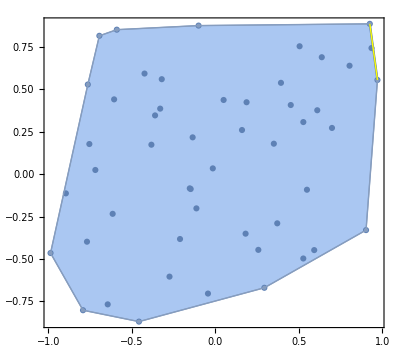

#### Test 3D

Module[{pts, px, py, pz, convexhull, convexhullmesh, paretoset, paretoindices, highlightcellindices, rbch, rect, f, d},
 pts = RandomReal[{-1, 1}, {50, 3}];
 
 DominatesQ[p1_, p2_] := And @@ ((First[#] > Last[#]) & /@ Transpose[{p1, p2}]);
 
 convexhullmesh = ConvexHullMesh[pts];
 convexhull = MeshCoordinates[convexhullmesh];
 
 paretoset = Complement[
   convexhull,
   Select[Tuples[convexhull, 2], DominatesQ[First[#], Last[#]] &][[All, 2]]
   ];
 
 paretoindices = Echo[Flatten[paretoset /. PositionIndex[convexhull]]];
 
 highlightcellindices = Echo[
   MeshCellIndex[
    convexhullmesh,
    Select[
     Union[
      MeshCells[convexhullmesh, 1],
      MeshCells[convexhullmesh, 2]
      ],
     SubsetQ[paretoindices, First[Level[#, 1]]] &
     ]
    ]
   ];
 
 GraphicsColumn[{
   Show[
    ListPointPlot3D[pts, PlotRange -> {{-1, 1}, {-1, 1}, {-1, 1}}, AspectRatio -> 1],
    HighlightMesh[ConvexHullMesh[pts, MeshCellStyle -> Opacity[0.01]], Style[#, Opacity[0.7]] & /@ highlightcellindices, PlotTheme -> "Detailed"],
    Graphics3D[{Red, Point[paretoset]}]
    ]
   }]
 ]

{17,6,7,11,19,13,1,22}

{{1,2},{1,34},{1,20},{1,62},{1,11},{1,19},{1,61},{1,29},{1,1},{1,10},{1,58},{1,18},{1,59},{1,3},{1,60},{2,4},{2,40},{2,36},{2,39},{2,1},{2,37},{2,8},{2,38}}

-Graphics-